## Fixed M_Z'=10 TeV, Fixed Brane parameter = 0.9, Vary parameter C_ν_Ri^Z'

Γ (Z'→ν ν̄) =  (g_PQ^2 M_(Z '))/(12π) ((1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2+(1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2+2 m_ν^2/(M_(Z ')^2) (  (1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2-2 ( (1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2 )√(1-4 m_ν^2/M_Z'^2)

```mathematica
MassZprime10=10;
MassNu=0.1;
CvL09=-1/4(e^2/(sinsquared(1-sinsquared)))(0.001)+(0.9)
```

0.899871

```mathematica
Zprime10decayfixedmass09[CvR_]:=MassZprime10/(12π)(1/4(CvL09+CvR)^2+1/4(CvL09-CvR)^2+2(MassNu/MassZprime10)^2(1/4(CvL09+CvR)^2-1/2(CvL09+CvR)^2))√(1-4(MassNu/MassZprime10)^2)*10^3
Qmax=1.0;
Qmin=0.0;
Npt=10;
Q[i_]:=(Qmax-Qmin)/Npt*i+Qmin
```

```mathematica
Zprime10decayfixedmass09Table=Table[{Q[i],Zprime10decayfixedmass09[Q[i]]},{i,0,Npt}]
```

{{0.,107.367},{0.1,108.69},{0.2,112.665},{0.3,119.292},{0.4,128.571},{0.5,140.502},{0.6,155.084},{0.7,172.319},{0.8,192.205},{0.9,214.742},{1.,239.932}}

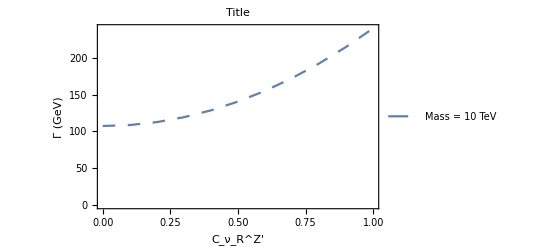

```mathematica
PlotZprimeDecayFixed1009=ListPlot[%, Joined-> True,PlotStyle->{Dashing[Medium]},PlotLegends->{"Mass = 10 TeV"},Frame->True,FrameLabel->{"C_ν_R^Z'","Γ (GeV)"},PlotLabel->HoldForm[Title],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

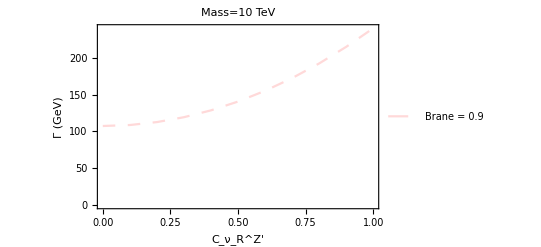

```mathematica
PlotZprimeDecayFixed1009B=ListPlot[%%, Joined-> True,PlotStyle->{LightRed,Dashing[Medium]},PlotLegends->{"Brane = 0.9"},Frame->True,FrameLabel->{"C_ν_R^Z'","Γ (GeV)"},PlotLabel->HoldForm[Mass = 10 TeV],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

```mathematica
TableForm[Zprime10decayfixedmass09Table,TableHeadings-> {None,{"CvR","Decay Rate(GeV)"}}]
```

CvR | Decay Rate(GeV)
0. | 107.367
0.1 | 108.69
0.2 | 112.665
0.3 | 119.292
0.4 | 128.571
0.5 | 140.502
0.6 | 155.084
0.7 | 172.319
0.8 | 192.205
0.9 | 214.742
1. | 239.932

## Fixed M_Z'=8 TeV, Fixed Brane parameter = 0.9, Vary parameter C_ν_Ri^Z'

Γ (Z'→ν ν̄) =  (g_PQ^2 M_(Z '))/(12π) ((1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2+(1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2+2 m_ν^2/(M_(Z ')^2) (  (1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2-2 (1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2 )√(1-4 m_ν^2/M_Z'^2)

```mathematica
MassZprime8=8;
MassNu=0.1;
CvL09=-1/4(e^2/(sinsquared(1-sinsquared)))(0.001)+(0.9)
```

0.899871

```mathematica
Zprime8decayfixedmass09[CvR_]:=MassZprime8/(12π)(1/4(CvL09+CvR)^2+1/4(CvL09-CvR)^2+2(MassNu/MassZprime8)^2(1/4(CvL09+CvR)^2-1/2(CvL09+CvR)^2))√(1-4(MassNu/MassZprime8)^2)*10^3
Qmax=1.0;
Qmin=0.0;
Npt=10;
Q[i_]:=(Qmax-Qmin)/Npt*i+Qmin
```

```mathematica
Zprime8decayfixedmass09Table=Table[{Q[i],Zprime8decayfixedmass09[Q[i]]},{i,0,Npt}]
```

{{0.,85.8788},{0.1,86.9363},{0.2,90.1149},{0.3,95.4146},{0.4,102.835},{0.5,112.377},{0.6,124.04},{0.7,137.824},{0.8,153.729},{0.9,171.755},{1.,191.902}}

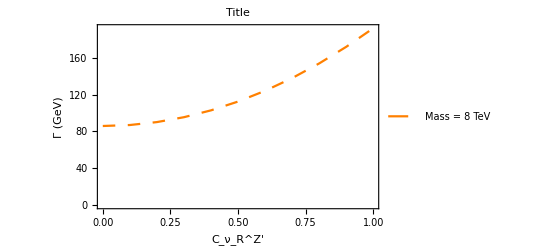

```mathematica
PlotZprimeDecayFixed809=ListPlot[%, Joined-> True,PlotStyle->{Orange, Dashing[Medium]},PlotLegends->{"Mass = 8 TeV"},Frame->True,FrameLabel->{"C_ν_R^Z'","Γ (GeV)"},PlotLabel->HoldForm[Title],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

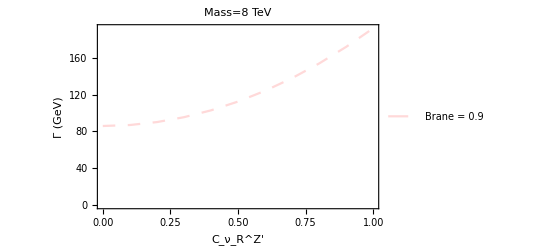

```mathematica
PlotZprimeDecayFixed809B=ListPlot[%%, Joined-> True,PlotStyle->{LightRed,Dashing[Medium]},PlotLegends->{"Brane = 0.9"},Frame->True,FrameLabel->{"C_ν_R^Z'","Γ (GeV)"},PlotLabel->HoldForm[Mass = 8 TeV],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

```mathematica
TableForm[Zprime8decayfixedmass09Table,TableHeadings-> {None,{"CvR","Decay Rate(GeV)"}}]
```

CvR | Decay Rate(GeV)
0. | 85.8788
0.1 | 86.9363
0.2 | 90.1149
0.3 | 95.4146
0.4 | 102.835
0.5 | 112.377
0.6 | 124.04
0.7 | 137.824
0.8 | 153.729
0.9 | 171.755
1. | 191.902

## Fixed M_Z'=5 TeV, Fixed Brane parameter = 0.9, Vary parameter C_ν_Ri^Z'

Γ (Z'→ν ν̄) =  (g_PQ^2 M_(Z '))/(12π) ((1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2+(1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2+2 m_ν^2/(M_(Z ')^2) (  (1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2-2 (1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2 )√(1-4 m_ν^2/M_Z'^2)

```mathematica
MassZprime5=5;
MassNu=0.1;
CvL09=-1/4(e^2/(sinsquared(1-sinsquared)))(0.001)+(0.9)
```

0.899871

```mathematica
Zprime5decayfixedmass09[CvR_]:=MassZprime5/(12π)(1/4(CvL09+CvR)^2+1/4(CvL09-CvR)^2+2(MassNu/MassZprime5)^2(1/4(CvL09+CvR)^2-1/2(CvL09+CvR)^2))√(1-4(MassNu/MassZprime5)^2)*10^3
Qmax=1.0;
Qmin=0.0;
Npt=10;
Q[i_]:=(Qmax-Qmin)/Npt*i+Qmin
```

```mathematica
Zprime5decayfixedmass09Table=Table[{Q[i],Zprime5decayfixedmass09[Q[i]]},{i,0,Npt}]
```

{{0.,53.635},{0.1,54.2925},{0.2,56.2748},{0.3,59.5818},{0.4,64.2135},{0.5,70.1699},{0.6,77.4509},{0.7,86.0567},{0.8,95.9872},{0.9,107.242},{1.,119.822}}

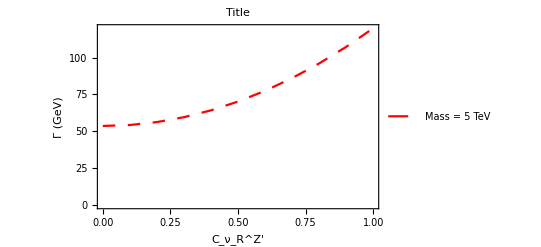

```mathematica
PlotZprimeDecayFixed509=ListPlot[%, Joined-> True,PlotStyle->{Red, Dashing[Medium]},PlotLegends->{"Mass = 5 TeV"},Frame->True,FrameLabel->{"C_ν_R^Z'","Γ (GeV)"},PlotLabel->HoldForm[Title],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

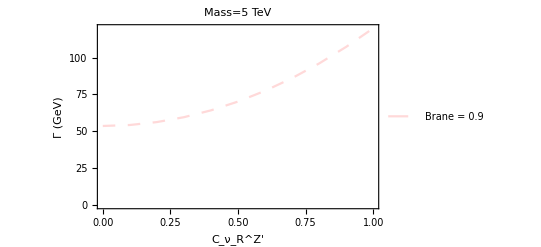

```mathematica
PlotZprimeDecayFixed509B=ListPlot[%%, Joined-> True,PlotStyle->{LightRed,Dashing[Medium]},PlotLegends->{"Brane = 0.9"},Frame->True,FrameLabel->{"C_ν_R^Z'","Γ (GeV)"},PlotLabel->HoldForm[Mass = 5 TeV],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

```mathematica
TableForm[Zprime5decayfixedmass09Table,TableHeadings-> {None,{"CvR","Decay Rate(GeV)"}}]
```

CvR | Decay Rate(GeV)
0. | 53.635
0.1 | 54.2925
0.2 | 56.2748
0.3 | 59.5818
0.4 | 64.2135
0.5 | 70.1699
0.6 | 77.4509
0.7 | 86.0567
0.8 | 95.9872
0.9 | 107.242
1. | 119.822

## OverLay

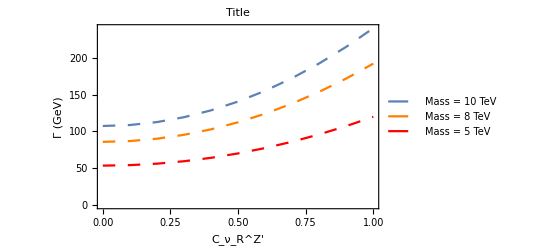

```mathematica
Show[PlotZprimeDecayFixed1009,PlotZprimeDecayFixed809,PlotZprimeDecayFixed509]
```

## OverLay 2

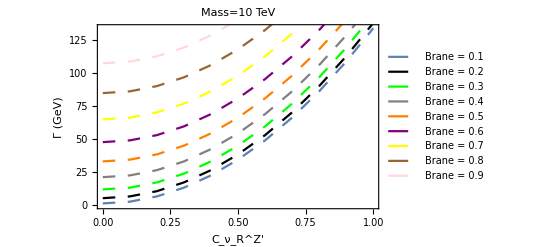

```mathematica
Show[PlotZprimeDecayFixed1001B,PlotZprimeDecayFixed1002B,PlotZprimeDecayFixed1003B,PlotZprimeDecayFixed1004B,PlotZprimeDecayFixed1005B,PlotZprimeDecayFixed1006B,PlotZprimeDecayFixed1007B,PlotZprimeDecayFixed1008B,PlotZprimeDecayFixed1009B]
```

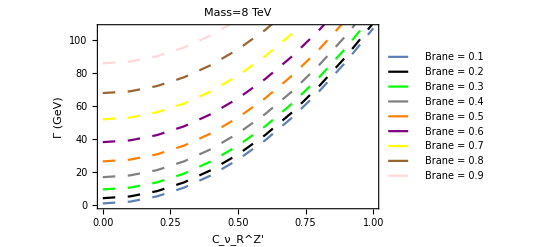

```mathematica
Show[PlotZprimeDecayFixed801B,PlotZprimeDecayFixed802B,PlotZprimeDecayFixed803B,PlotZprimeDecayFixed804B,PlotZprimeDecayFixed805B,PlotZprimeDecayFixed806B,PlotZprimeDecayFixed807B,PlotZprimeDecayFixed808B,PlotZprimeDecayFixed809B]
```

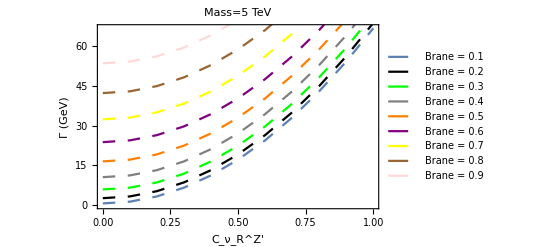

```mathematica
Show[PlotZprimeDecayFixed501B,PlotZprimeDecayFixed502B,PlotZprimeDecayFixed503B,PlotZprimeDecayFixed504B,PlotZprimeDecayFixed505B,PlotZprimeDecayFixed506B,PlotZprimeDecayFixed507B,PlotZprimeDecayFixed508B,PlotZprimeDecayFixed509B]
```